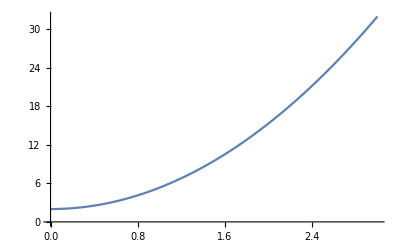

```mathematica
Plot[10/3 *(x^2 + 3/5),{x,0,3}]
```

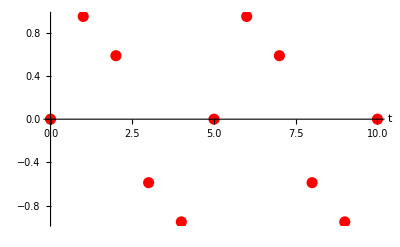

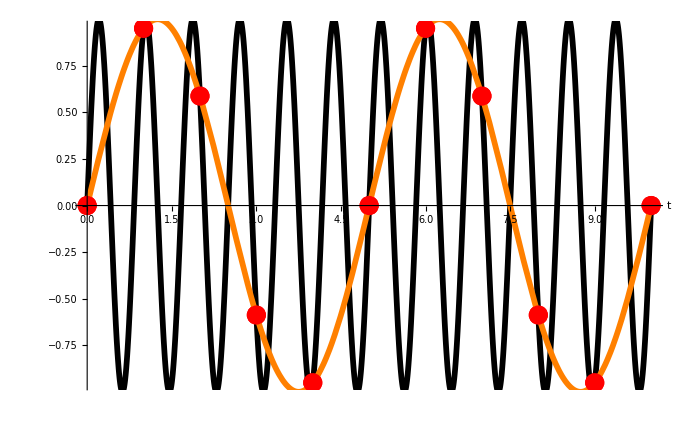

```mathematica
fOne[x_]:=Sin[0.2 * 2 Pi x]
fTwo[x_]:=Sin[1.2 * 2 Pi x]
fS = 1;
dt = 1/fS;
samplePoints =Range[0,10,dt];
samples = fTwo[#]&/@samplePoints;

p1=ListPlot[Partition[Riffle[samplePoints,samples],2],PlotStyle->Directive[Red,PointSize[0.02]],AxesLabel->{"t",None},TicksStyle->Large,LabelStyle->Large,TicksStyle->Directive[Black,5]]
p2=Plot[fTwo[x],{x,0,10},PlotStyle->Directive[Black,Thickness[0.006]],TicksStyle->Directive[Black,5]];
p3=Plot[fOne[x],{x,0,10},PlotStyle->Directive[Orange,Thickness[0.006]],TicksStyle->Directive[Black,5]];
Show[p1,p2,p3,p1]
```